# Tracking evolution of domains during von-Neumann evolution

Here we analyze the coarsening process of mesh patterns in the switch+PMB Min system.

## Import data

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Comsol2Mathematica2hdf5.nb",
InsertResults->False,
EvaluationElements->Automatic
];
```

```mathematica
times=Join[{0},10^Range[0,5.6,0.1]];
```

```mathematica
dataMesh=Import[NotebookDirectory[]<>"MinSwitchPMB-2Dflat-MinEmesh-vonNeumann1.txt","Comsol2DSweep"];
```

```mathematica
data=Partition[dataMesh["mde+me"],Length@times];
```

```mathematica
grid=dataMesh["Grid"];
```

```mathematica
dataMesh=Import[NotebookDirectory[]<>"MinSwitchPMB-2Dflat-MinEmesh-vonNeumann2.txt","Comsol2DSweep"];
```

```mathematica
data=Join[data,Partition[dataMesh["mde+me"],Length@times]];
```

```mathematica
dataMesh=Import[NotebookDirectory[]<>"MinSwitchPMB-2Dflat-MinEmesh-vonNeumann3.txt","Comsol2DSweep"];
```

```mathematica
data=Join[data,Partition[dataMesh["mde+me"],Length@times]];
```

MinD density for example plot

```mathematica
dataMesh=Import[NotebookDirectory[]<>"MinSwitchPMB-2Dflat-MinD-vonNeumann1.txt","Comsol2DSweep"];
dataMinD=Partition[dataMesh["mde+md"],Length@times];
```

## Data visualization

```mathematica
Manipulate[Image[data[[Floor@sim,Floor@i]]]//ImageAdjust,{i,1,Length@data[[1]]},{sim,1,Length@data}]
```

```mathematica
Manipulate[Thinning[Binarize[Image[data[[Floor@sim,Floor@i]]]//ImageAdjust,0.1],Padding->1],{i,1,Length@times},{sim,1,Length@data}]
```

```mathematica
Manipulate[MorphologicalComponents[ImagePad[Thinning[Binarize[Image[data[[Floor@sim,Floor@i]]]//ImageAdjust,0.1],Padding->1],1]//ColorNegate,CornerNeighbors->False]//Colorize,{i,1,Length@times},{sim,1,Length@data}]
```

### Example patterns

```mathematica
colorMap={minD/1.5,minE,minE+minD/1.5/1.5};
```

```mathematica
ind=12;
times[[ind]]
ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@Image/@{data[[1,ind]],dataMinD[[1,ind]]}))
```

10.

-Graphics-

```mathematica
ind=25;
times[[ind]]
ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@Image/@{data[[1,ind]],dataMinD[[1,ind]]}))
```

199.526

-Graphics-

```mathematica
ind=32;
times[[ind]]
ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@Image/@{data[[1,ind]],dataMinD[[1,ind]]}))
```

1000.

-Graphics-

```mathematica
ind=52;
times[[ind]]
ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@Image/@{data[[1,ind]],dataMinD[[1,ind]]}))
```

100000.

-Graphics-

## Measure domains

```mathematica
domains=Table[Table[Block[{
mesh=ImagePad[Thinning[Binarize[Image[frame]//ImageAdjust,0.1],Padding->1],1],
morphComps,
meas,
branchPoints,
cornerNumbers
},
morphComps=MorphologicalComponents[mesh//ColorNegate,CornerNeighbors->False];
meas=SortBy[ComponentMeasurements[morphComps,{"Centroid","Area"}],Values[#][[2]]&][[;;-2]];
branchPoints=MorphologicalBranchPoints[mesh];
Table[With[{mask=Dilation[Map[If[#==domain,1,0]&,morphComps,{2}],DiskMatrix[1]]},
{
First[domain/.meas],
Last[domain/.meas],
Total@Flatten[mask*ImageData[branchPoints]]
}
],
{domain,Keys@meas}]
],
{frame,sim}],{sim,data}];
```

## Track domains

Collect domains found in each frame into time tracks of single domains moving around in the system

```mathematica
domainTracks=Table[{{times[[1]],#}}&/@(dom[[1]]),{dom,domains}];
Monitor[Do[Do[Block[{
doms=domains[[simInd,i]],
time=times[[i]],
timePrev=times[[i-1]],
distances,
distancesSorted
},
Do[
distances=Transpose@{Range[Length[domainTracks[[simInd]]]],If[#[[-1,1]]==timePrev,Norm[domain[[1]]-#[[-1,2,1]]],Infinity]&/@domainTracks[[simInd]]};
distancesSorted=SortBy[distances,#[[2]]&];
If[distancesSorted[[1,2]]<20&&distancesSorted[[2,2]]>20 &&domainTracks[[simInd,distancesSorted[[1,1]],-1,2,3]]==domain[[3]],(*ensure that only one junction from the previous time is close to the one we are looking at at the current time;
start new track also if the number of corners changes*)
AppendTo[domainTracks[[simInd,distancesSorted[[1,1]]]],{time,domain}],
AppendTo[domainTracks[[simInd]],{{time,domain}}](*start a new track*)
];
,{domain,doms}]
],{i,2,Length@times}],{simInd,Length@data}];,{simInd,i}]
domainTracks=Flatten[domainTracks,1];
```

#### Initial distribution

Factor (100/300) scales pixels to length units of the simulation;
Moreover, areas are scaled by a factor 1/2 in the simultion

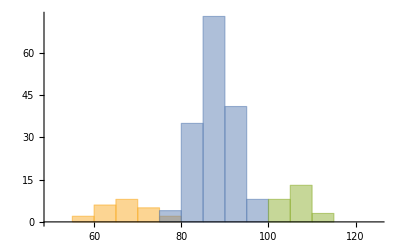

```mathematica
Histogram[(100/300)^2/2{
Select[Flatten[domains[[All,1]],1],#[[3]]==5&][[All,2]],
Select[Flatten[domains[[All,1]],1],#[[3]]==6&][[All,2]],
Select[Flatten[domains[[All,1]],1],#[[3]]==7&][[All,2]]
},{50,125,5}]
```

```mathematica
(100/300)^2/2Mean/@{
Select[Flatten[domains[[All,1]],1],#[[3]]==5&][[All,2]],
Select[Flatten[domains[[All,1]],1],#[[3]]==6&][[All,2]],
Select[Flatten[domains[[All,1]],1],#[[3]]==7&][[All,2]]
}
```

{66.8741,87.8387,105.682}

#### Final distribution

```mathematica
Log10@times[[-1]]
```

5.6

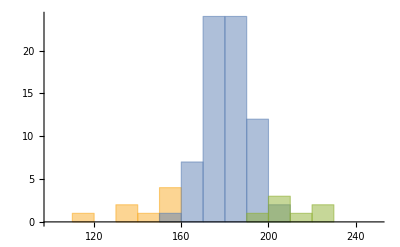

```mathematica
Histogram[(100/300)^2/2{
Select[Flatten[domains[[All,-1]],1],#[[3]]==5&][[All,2]],
Select[Flatten[domains[[All,-1]],1],#[[3]]==6&][[All,2]],
Select[Flatten[domains[[All,-1]],1],#[[3]]==7&][[All,2]]
},{100,250,10}]
```

```mathematica
(100/300)^2/2Mean/@{
Select[Flatten[domains[[All,-1]],1],#[[3]]==5&][[All,2]],
Select[Flatten[domains[[All,-1]],1],#[[3]]==6&][[All,2]],
Select[Flatten[domains[[All,-1]],1],#[[3]]==7&][[All,2]]
}
```

{142.35,181.6,210.831}

Compare initial (scaled by 2) and final distributions

```mathematica
Histogram[(100/300)^2{
Select[Flatten[domains[[All,1]],1],#[[3]]==5&][[All,2]]*2,
Select[Flatten[domains[[All,1]],1],#[[3]]==6&][[All,2]]*2,
Select[Flatten[domains[[All,1]],1],#[[3]]==7&][[All,2]]*2,
Select[Flatten[domains[[All,-1]],1],#[[3]]==5&][[All,2]],
Select[Flatten[domains[[All,-1]],1],#[[3]]==6&][[All,2]],
Select[Flatten[domains[[All,-1]],1],#[[3]]==7&][[All,2]]
},{200,500,10},ChartStyle->{Lighter@Lighter@Blue,Blue,Darker@Green,Red,Black,Purple},ChartLayout->{"Row",UpTo[2]}]
```

-Graphics-

#### Domain-size dynamics

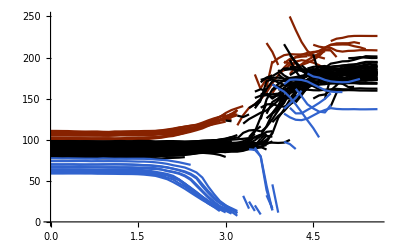

```mathematica
Show[
ListLinePlot[({Log10@#[[1]],(100/300)^2/2*#[[2,2]]}&/@#)&/@Select[domainTracks[[;;;;2]],#[[1,2,3]]==7&],PlotStyle->Darker@RGBColor[{202,51,0}/255],PlotRange->{0,250}],
ListLinePlot[({Log10@#[[1]],(100/300)^2/2*#[[2,2]]}&/@#)&/@Select[domainTracks[[;;;;2]],#[[1,2,3]]==6&],PlotStyle->Black,PlotRange->All],
ListLinePlot[({Log10@#[[1]],(100/300)^2/2*#[[2,2]]}&/@#)&/@Select[domainTracks[[;;;;2]],#[[1,2,3]]==5&],PlotStyle->RGBColor[{49,99,206}/255],PlotRange->All]
]
```

#### Initial period: Coarsening

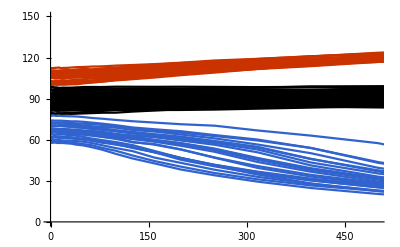

```mathematica
Show[
ListLinePlot[(Transpose[{#[[All,1]],(100/300)^2/2*#[[All,2,2]]}])&/@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==6&],PlotStyle->Black,PlotRange->{{0,500},{0,150}}],
ListLinePlot[(Transpose[{#[[All,1]],(100/300)^2/2*#[[All,2,2]]}])&/@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==5&],PlotStyle->RGBColor[{49,99,206}/255]],
ListLinePlot[(Transpose[{#[[All,1]],(100/300)^2/2*#[[All,2,2]]}])&/@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==7&],PlotStyle->RGBColor[{202,51,0}/255]]
]
```

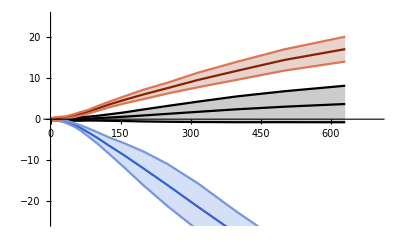

```mathematica
Show[
ListLinePlot[{
(Transpose[{#[[1,All,1]],(100/300)^2/2*Mean[Select[#,Max[Abs@#]<1000&]]&@(#[[All,All,2,2]]-#[[All,1,2,2]])}])&@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==6&][[All,;;30]],
(Transpose[{#[[1,All,1]],(100/300)^2/2*(Mean[Select[#,Max[Abs@#]<1000&]]+StandardDeviation[Select[#,Max[#]<1000&]])&@(#[[All,All,2,2]]-#[[All,1,2,2]])}])&@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==6&][[All,;;30]],
(Transpose[{#[[1,All,1]],(100/300)^2/2*(Mean[Select[#,Max[Abs@#]<1000&]]-StandardDeviation[Select[#,Max[#]<1000&]])&@(#[[All,All,2,2]]-#[[All,1,2,2]])}])&@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==6&][[All,;;30]]},PlotStyle->Black,PlotRange->{{0,700},{-25,25}},Filling->{1->{2},1->{3}}],
ListLinePlot[{
(Transpose[{#[[1,All,1]],(100/300)^2/2*Mean[Select[#,Max[Abs@#]<1000&]]&@(#[[All,All,2,2]]-#[[All,1,2,2]])}])&@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==5&][[All,;;30]],
(Transpose[{#[[1,All,1]],(100/300)^2/2*(Mean[Select[#,Max[Abs@#]<1000&]]+StandardDeviation[Select[#,Max[#]<1000&]])&@(#[[All,All,2,2]]-#[[All,1,2,2]])}])&@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==5&][[All,;;30]],
(Transpose[{#[[1,All,1]],(100/300)^2/2*(Mean[Select[#,Max[Abs@#]<1000&]]-StandardDeviation[Select[#,Max[#]<1000&]])&@(#[[All,All,2,2]]-#[[All,1,2,2]])}])&@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==5&][[All,;;30]]},PlotStyle->{RGBColor[{49,99,206}/255],Lighter@RGBColor[{49,99,206}/255],Lighter@RGBColor[{49,99,206}/255]},Filling->{1->{2},1->{3}}],
ListLinePlot[{
(Transpose[{#[[1,All,1]],(100/300)^2/2*Mean[Select[#,Max[Abs@#]<1000&]]&@(#[[All,All,2,2]]-#[[All,1,2,2]])}])&@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==7&][[All,;;30]],
(Transpose[{#[[1,All,1]],(100/300)^2/2*(Mean[Select[#,Max[Abs@#]<1000&]]+StandardDeviation[Select[#,Max[#]<1000&]])&@(#[[All,All,2,2]]-#[[All,1,2,2]])}])&@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==7&][[All,;;30]],
(Transpose[{#[[1,All,1]],(100/300)^2/2*(Mean[Select[#,Max[Abs@#]<1000&]]-StandardDeviation[Select[#,Max[#]<1000&]])&@(#[[All,All,2,2]]-#[[All,1,2,2]])}])&@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==7&][[All,;;30]]},PlotStyle->{Darker@RGBColor[{202,51,0}/255],Lighter@RGBColor[{202,51,0}/255],Lighter@RGBColor[{202,51,0}/255]},Filling->{1->{2},1->{3}}]
]
```

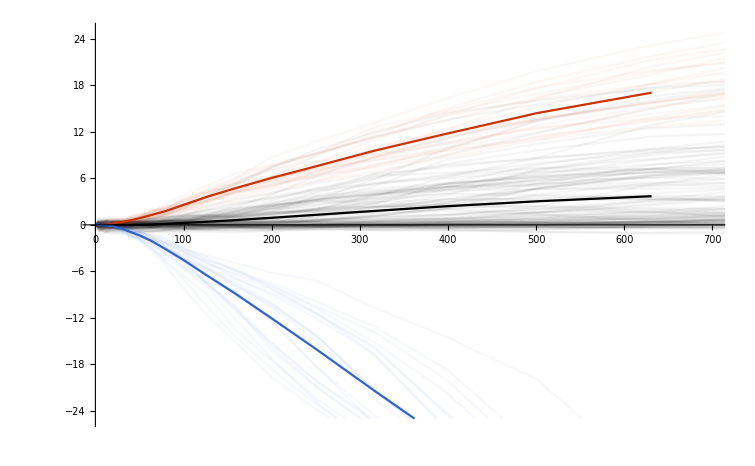

```mathematica
Show[
ListLinePlot[{
(Transpose[{#[[1,All,1]],(100/300)^2/2*Mean[Select[#,Max[Abs@#]<1000&]]&@(#[[All,All,2,2]]-#[[All,1,2,2]])}])&@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==6&][[All,;;30]]},PlotStyle->Black,PlotRange->{{0,700},{-25,25}}],
ListLinePlot[(Transpose[{#[[All,1]],(100/300)^2/2*(#[[All,2,2]]-#[[1,2,2]])}])&/@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==6&],PlotStyle->RGBColor[{0,0,0,0.04}],PlotRange->{{0,700},{-25,25}}],
ListLinePlot[{
(Transpose[{#[[1,All,1]],(100/300)^2/2*Mean[Select[#,Max[Abs@#]<1000&]]&@(#[[All,All,2,2]]-#[[All,1,2,2]])}])&@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==7&][[All,;;30]]},PlotStyle->RGBColor[{202,51,0,255}/255],PlotRange->{{0,700},{-25,25}}],
ListLinePlot[(Transpose[{#[[All,1]],(100/300)^2/2*(#[[All,2,2]]-#[[1,2,2]])}])&/@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==7&],PlotStyle->RGBColor[{202,51,0,0.04*255}/255],PlotRange->{{0,700},{-25,25}}],
ListLinePlot[{
(Transpose[{#[[1,All,1]],(100/300)^2/2*Mean[Select[#,Max[Abs@#]<1000&]]&@(#[[All,All,2,2]]-#[[All,1,2,2]])}])&@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==5&][[All,;;30]]},PlotStyle->RGBColor[{49,99,206,255}/255],PlotRange->{{0,700},{-25,25}}],
ListLinePlot[(Transpose[{#[[All,1]],(100/300)^2/2*(#[[All,2,2]]-#[[1,2,2]])}])&/@Select[domainTracks,Length[#]>30&&#[[1,1]]==times[[1]]&&#[[1,2,3]]==5&],PlotStyle->RGBColor[{49,99,206,0.04*255}/255],PlotRange->{{0,700},{-25,25}}]
]
```